### Setup

```mathematica
Needs["Calendar`"]
```

```mathematica
Off[NumberForm::"sigz"]
fixnum[n_]:=n//Chop//N[#,17]&//NumberForm[#,17, ExponentStep->9]&
SetAttributes[fixnum,Listable];
```

```mathematica
(* Note that a year BC is n-1 in the year field (1 BC is year==0,69 BC is year==68): *)
dateFromRDD[-1]
DaysBetween[rataDieDay0, {-1,12,31},Calendar->Gregorian]
```

dateFromRDD[-1]

DaysBetween::datestruct: To be a valid date, the argument rataDieDay0 must have the form {y, m, d} or {y, m, d, h, mn, s}, where y, m, and d are all integers.

DaysBetween[rataDieDay0,{-1,12,31},Calendar→Gregorian]

### Julian Day, Rata Die, and Rata Die Seconds

```mathematica
(* Rata Die Day to and from Date *)
rataDieDay0={0,12,31};
dateFromRDD[rd_]:=Flatten[{DaysPlus[rataDieDay0,rd,Calendar->Gregorian],
Floor[24Mod[rd,1]],Floor[Mod[60*24rd,1]],Floor[60*60*24Mod[rd,1]]},1]
rddFromDate[{y_,m_,d_,h_:0,min_:0,s_:0}]:=
DaysBetween[rataDieDay0, {y,m,d},Calendar->Gregorian]+ (h+(min+(s/60))/60)/24
rddFromDate[Null]= {NULL,NULL,NULL};
(* Julian Day to and from Date *)
julianDay0 =CalendarChange[{-4712,1,1,12,0,0},Julian,Gregorian];
jdFromDate[{y_,m_,d_,h_:0,min_:0,s_:0}]:=
DaysBetween[julianDay0, {y,m,d},Calendar->Gregorian] + (h+(min+(s/60))/60)/24
dateFromJD[jd_]:=
DaysPlus[julianDay0,Floor[jd]//Rationalize,Calendar->Gregorian]+
{0,0,0,Floor[24Mod[jd,1]],Floor[Mod[60*24jd,1]],Floor[Mod[60*60*24*jd,1]]}
(* Convert JD to RD and RDs*)
secsFromDays[x_]:=x*(24*60*60)
daysFromSecs[x_]:=x/(24*60*60)
jdFromRDD  [rd_]  :=rd-(rddFromDate[julianDay0])
rddFromJD[jd_]  :=jd+(rddFromDate[julianDay0])
jdFromRDS[rds_]:=jdFromRDD[daysFromSecs[rds]]
rdsFromJD[jd_]  :=secsFromDays[rddFromJD[jd]]
(* Make a range of dates *)
dayRange[d0_, d1_,a_:1] := dateFromRDD/@Range[rddFromDate[d0],rddFromDate[d1],a]
```

```mathematica
rddFromJD[0]
```

-3442849/2

```mathematica
{jdFromRDS[rdsFromJD[321546]],rddFromJD[jdFromRDD[321546]]}; (*Check*)
{jdFromDate[{1993,5,21}],
jdFromDate[{1993,5,21,12,13,6}],
jdFromDate[{1993,5,21}]+.5+(13.1/(24*60)),
jdFromDate[{2007,1,1}],
jdFromDate[{2000,1,6,18,15,0}],2451550.260
dateFromJD[jdFromDate[{1993,5,21}]],
dateFromJD[jdFromDate[julianDay0]]
}//fixnum//TableForm;
```

### Other Calendars

Convert into each Available calendar.

```mathematica
calendarTypes={Julian, Islamic, Jewish};
otherCals[d_]:=Module[{rd,jul,isl,heb,juGrDiff},
{jul,isl,heb}= (CalendarChange[d,Gregorian, #]&/@calendarTypes);
rd=rddFromDate[d];
juGrDiff=rd-rddFromDate[jul];
Flatten[{rd,{d},{jul,isl,heb},juGrDiff},1]];
```

```mathematica
(otherCals/@dayRange[{1800,1,1},{1900,2,2},3650])//Transpose//MatrixForm
```

(657072 | 660722 | 664372 | 668022 | 671672 | 675322 | 678972 | 682622 | 686272 | 689922 | 693572
{1800,1,1,0,0,0} | {1809,12,30,0,0,0} | {1819,12,28,0,0,0} | {1829,12,25,0,0,0} | {1839,12,23,0,0,0} | {1849,12,20,0,0,0} | {1859,12,18,0,0,0} | {1869,12,15,0,0,0} | {1879,12,13,0,0,0} | {1889,12,10,0,0,0} | {1899,12,8,0,0,0}
{1799,12,21,0,0,0} | {1809,12,18,0,0,0} | {1819,12,16,0,0,0} | {1829,12,13,0,0,0} | {1839,12,11,0,0,0} | {1849,12,8,0,0,0} | {1859,12,6,0,0,0} | {1869,12,3,0,0,0} | {1879,12,1,0,0,0} | {1889,11,28,0,0,0} | {1899,11,26,0,0,0}
{1214,8,4,0,0,0} | {1224,11,23,0,0,0} | {1235,3,11,0,0,0} | {1245,6,28,0,0,0} | {1255,10,16,0,0,0} | {1266,2,4,0,0,0} | {1276,5,23,0,0,0} | {1286,9,11,0,0,0} | {1296,12,28,0,0,0} | {1307,4,16,0,0,0} | {1317,8,4,0,0,0}
{5560,10,4,0,0,0} | {5570,10,23,0,0,0} | {5580,10,10,0,0,0} | {5590,9,29,0,0,0} | {5600,10,16,0,0,0} | {5610,10,5,0,0,0} | {5620,9,22,0,0,0} | {5630,10,11,0,0,0} | {5640,9,28,0,0,0} | {5650,9,17,0,0,0} | {5660,10,6,0,0,0}
11 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12)

```mathematica
(*otherCalsBigTable=(otherCals/@dayRange[
CalendarChange[{1,1,1}, Jewish, Gregorian],
{5000,12,31},
1]);
Export["calendarinfo-othercals-mathematica.csv",Prepend[
Flatten/@(otherCalsBigTable),
{"rataDie",
"julYear","julMonth","julDay",
"islYear","islMonth","islDay",
"hebYear","hebMonth","hebDay",
"offsetGreJul"
}], "CSV"]*)
```

### Info about each year

```mathematica
yearInfo[y_]:={rddFromDate[#],#}&/@{EasterSunday[y], EasterSundayGreekOrthodox[y], If[y<1900, Null,JewishNewYear[y]]};
```

```mathematica
(yearInfo/@Range[1900,2000,10])//Transpose//MatrixForm
```

((693700
{1900,4,15}) | (697333
{1910,3,27}) | (700994
{1920,4,4}) | (704662
{1930,4,20}) | (708288
{1940,3,24}) | (711956
{1950,4,9}) | (715617
{1960,4,17}) | (719250
{1970,3,29}) | (722911
{1980,4,6}) | (726572
{1990,4,15}) | (730233
{2000,4,23})
(693707
{1900,4,22}) | (697368
{1910,5,1}) | (701001
{1920,4,11}) | (704662
{1930,4,20}) | (708323
{1940,4,28}) | (711956
{1950,4,9}) | (715617
{1960,4,17}) | (719278
{1970,4,26}) | (722911
{1980,4,6}) | (726572
{1990,4,15}) | (730240
{2000,4,30})
(693862
{1900,9,24}) | (697524
{1910,10,4}) | (701156
{1920,9,13}) | (704818
{1930,9,23}) | (708481
{1940,10,3}) | (712112
{1950,9,12}) | (715775
{1960,9,22}) | (719436
{1970,10,1}) | (723069
{1980,9,11}) | (726730
{1990,9,20}) | (730393
{2000,9,30}))

```mathematica
(*yearInfoBigTable=yearInfo/@Range[1,5000,1];
Export["calendarinfo-lunarcalDates-mathematica.csv",Prepend[Flatten/@(yearInfoBigTable),{"easterRD","easterYear","easterMonth","easterDay",
"orthEasterRD","orthEasterYear","orthEasterMonth","orthEasterDay",
"hebNewYearRD","hebNewYearYear","hebNewYearMonth","hebNewYearDay"
}], "CSV"]*)
```

### Lunation Index

#### Moon from index: First order

```mathematica
(* 
From http://scienceworld.wolfram.com/astronomy/NewMoon.html, but numbering from lunation 1 is first new moon of year 1 instead of year 1923.
There is a mistake:the formula should be
2423407.0814 + 29.53058868632136 * n
and not
2449128.59   + 29.53058867 * n
*)
jdfromSMandN[synMonthLen_,n1_]:=2423407.0814+synMonthLen *(n1-23771)
jdFromN[n1_]:=jdfromSMandN[29.53058868632136,n1]//Simplify;
approxNewmoonEqn ={
jd==jdFromN[n1 ], 
n1==n1923+23771,
rataDieSecs==rdsFromJD[jd]
}//Simplify
rdsFromN[n_]:=(rataDieSecs/.Solve[approxNewmoonEqn, rataDieSecs, {n1923,jd}]//
First//Simplify)/.{n1->n}
nEstFromRDS [rds_]:=(n1/.                            Solve[approxNewmoonEqn, n1,                         {n1923,jd}]//
First//Simplify)/.{rataDieSecs->rds}
nEstFromJD[ajd_]:=(n1/.                            Solve[approxNewmoonEqn, n1,                         {n1923,rataDieSecs}]//
First//Simplify)/.{jd->ajd}
{rdsFromN[n1], nEstFromRDS[rds],nEstFromJD[jd]}//fixnum//MatrixForm
```

{jd==1.72144×10^6+29.5306 n1,n1==23771+n1923,rataDieSecs==43200 (-3442849+2 jd)}

(946748.516113281+2551442.862498166 n1
-371063969.3485072×10^-9+(391.9350947255316×10^-9) rds
-58293.29973820766+(33863192.18428593×10^-9) jd)

```mathematica
Jan 13 10:57
```

```mathematica
rdsFromNSimple[n_]:=( (11.4563)+29.5305888531*n  )* 60*60*24
rdsFromNSimple[n]
rdsFromNSimple[n]//Simplify
rdsFromN[n]/(60*60*24)//Simplify
rdsFromN[n]-rdsFromNSimple[n]//Simplify
```

86400 (11.4563+29.5306 n)

989824.+2.55144×10^6 n

10.9577+29.5306 n

-43075.8-0.0144097 n

```mathematica
(2423407.0814-1721424.5)+29.53058868632136 *(n1-23771)//Simplify
```

10.9577+29.5306 n1

```mathematica
CalendarChange[{1,1,13},Julian,Gregorian]
11.42629629629664-.5//fixnum
rddFromDate[julianDay0]//N//fixnum
```

{1,1,11}

10.92629629629664

-1721424.5

```mathematica
Solve[n1+23771==nEstFromJD[jd],jd]//Simplify//fixnum
Solve[n1+23771==nEstFromRDS[jd]+0.36326014514322635*(24*60*60),jd]//Simplify//fixnum
```

{{jd→2423407.0814+29.53058868632136 n1}}

{{jd→-19.42746536065527×10^9+2551442.862498166 n1}}

#### Synodic Month

```mathematica
synMonthJD[jd_]:=(29.5305888531+0.00000021621*T-3.64 10^-10*T^2)/.T->((jd-2451545.0)/36525)
nIntegratedFromJDEqn=0+
(∫_jdFromN[0]^jd1 1/(synMonthJD[jdi])ⅆjdi//Refine[#,{jd1∈Reals,-1.0390113417408892*^10≤jd1≤1.0416711755348454*^10}]&)
nIntegratedFromJD[jd_]:=nIntegratedFromJDEqn/.jd1->jd
rdsIntegratedFromNEqn=rds/.Solve[{n1==nIntegratedFromJDEqn,rds==rdsFromJD[jd1]},rds, {jd1}]//First
rdsIntegratedFromN[n_]:=rdsIntegratedFromNEqn/.n1->n
```

392059.-1.76146×10^8 Log[1.04167×10^10-1. jd1]+1.76146×10^8 Log[1.03901×10^10+jd1]

(-4.06222×10^27+4.06222×10^27 ⅇ^(5.6771×10^-9 n1))/(4.52436×10^12+4.51431×10^12 ⅇ^(5.6771×10^-9 n1))

```mathematica
rdsFromN
```

rdsFromN

```mathematica
{rdsIntegratedFromN[0],rdsFromN[0],(secsFromDays[11.4262963])}
```

{946748.,946749.,987232.}

```mathematica
rdsIntegratedFromN[nIntegratedFromJD[2451550]]
```

6.30828×10^10

#### pl

```mathematica
Plot[synMonthJD[jd],{jd,jdFromDate[{1,1,1}],jdFromDate[{2001,1,1}]}];
```

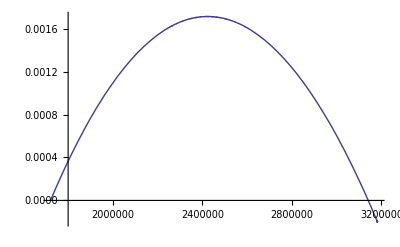

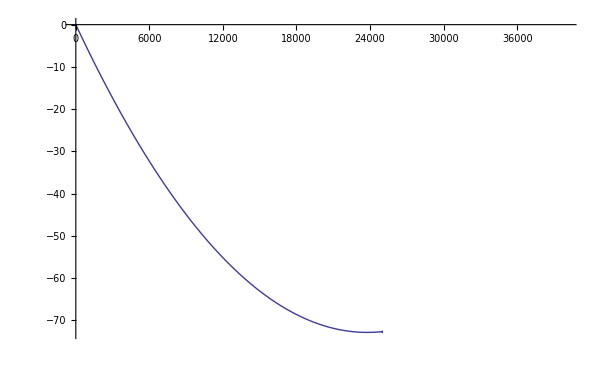

```mathematica
Plot[{nIntegratedFromJD[jd]-nEstFromJD[jd]},{jd,jdFromDate[{1,1,1}],jdFromDate[{4000,1,1}]}]
Plot[{(rdsIntegratedFromN[n ]-rdsFromN[n])/60},{n,0,25000}, ImageSize->600, PlotRange->{{0,40000},Automatic}]
```

```mathematica
Plot[synMonthJD[jd],
{jd,jdFromDate[{1,1,1}],jdFromDate[{2001,1,1}]}];
```

#### See

```mathematica
moonHeaders={"Synodic Month",
"Lunation from 12 jan 1","Acc Lun",
"Diff","Diff",
 "Julian Day", "Rata Die Day", "Rata Die Seconds", "Date"};
smFoo[jd_]:=Append[{
synMonthJD[jd], 
nEstFromRDS[rdsFromJD[jd]],nIntegratedFromJD[jd],
(nEstFromRDS[rdsFromJD[jd]]-nIntegratedFromJD[jd])*(60*24*60)/29.53 (*1000000/29.53*),
rdsFromN[nEstFromRDS[rdsFromJD[jd]]]-rdsIntegratedFromN[nEstFromRDS[rdsFromJD[jd]]],
jd, rddFromJD[jd], rdsFromJD[jd]
}//fixnum, 
dateFromJD[jd]];
{moonHeaders,
smFoo[jdFromDate[{1,1,11,10,48,52}]],
smFoo[jdFromDate[{500,12,18,12,13,6}]],
smFoo[jdFromDate[{1922,12,18,12,13,6}]],
smFoo[jdFromDate[{2003,12,23}]],
smFoo[jdFromDate[{2000,1,6,18,14,24}]],
smFoo[2451550.260]}//MatrixForm
```

(Synodic Month | Lunation from 12 jan 1 | Acc Lun | Diff | Diff | Julian Day | Rata Die Day | Rata Die Seconds | Date
29.53058438577004 | 16689961.78475196×10^-9 | 16689979.64588925×10^-9 | -52258.7965451298×10^-9 | 43594428.1052798×10^-9 | 1721435.950601852 | 11.45060185180046 | 989331.999995559 | {1,1,10,34,0,0}
29.53058553030733 | 6183.335974075815 | 6183.336755001161 | -2.284861156292596 | 1991.067890167236 | 1904033.009097222 | 182608.5090972222 | 15.777375186×10^9 | {500,12,18,12,0,0}
29.53058868632093 | 23770.99755159713 | 23770.99926444253 | -5.011508399617498 | 4370.330444335938 | 2423407.009097222 | 701982.5090972223 | 60.651288786×10^9 | {1922,12,18,12,0,0}
29.53058886169159 | 24772.99216867308 | 24772.99387904367 | -5.004267512463964 | 4362.763496398926 | 2452996.5 | 731572. | 63.2078208×10^9 | {2003,12,22,24,0,0}
29.53058885313113 | 24724.01786560847 | 24724.01957579813 | -5.003738126304673 | 4363.458564758301 | 2451550.26 | 730125.7599999998 | 63.08286566399998×10^9 | {2000,1,6,18,0,0}
29.53058885313113 | 24724.01786560847 | 24724.01957579813 | -5.003738126304673 | 4363.458564758301 | 2451550.26 | 730125.7599999998 | 63.08286566399998×10^9 | {2000,1,6,18,0,0})

### Checking Kronberg vs Perl

Bouncing C Kronberg
  http://www.maa.mhn.de/StarDate/
against 
  http://search.cpan.org/~dmaki/DateTime-Util-Astro-0.11001/lib/DateTime/Util/Astro/Moon.pm

#### Load

```mathematica
mqKron=Import["calendarinfo-kronberg-all.csv"];
mqPerl=Import["calendarinfo-moonquarters-21000-28000-cond.csv"];
mqPerlAll=Import["calendarinfo-moonquarters-all.csv"];
mqPerlHeader=Take[mqPerl,1];
mqPerl                =Drop[mqPerl,1];
```

#### Pivot

```mathematica
{nmkBegLun,nmkEndLun}={mqKron[[1,1]],mqKron[[-1,1]]};
{nmpBegLun,nmpEndLun}={mqPerl[[1,1]],mqPerl[[-1,1]]};
{begLun,endLun}={nmkBegLun,nmkEndLun};
(*{begLun,endLun}={22200,23100};*)
newmoonsPerl = Take[mqPerl[[All,{1,3}]],{1+begLun-nmpBegLun,1+endLun-nmpBegLun}];
newmoonsKron = Take[mqKron[[All,{1,3}]],{1+begLun-nmkBegLun,1+endLun-nmkBegLun}];
(* Look at what we hauled in *)
{{begLun,endLun,nmkBegLun,nmkEndLun, nmpBegLun,nmpEndLun},
Length/@{mqPerlHeader,mqPerl, newmoonsKron, newmoonsPerl},
{First[#],Last[#]}&/@{newmoonsKron, newmoonsPerl}}//MatrixForm
fooCull[mat_]:=Flatten[{mat[[1;;1+22238-nmpBegLun]],mat[[1+24562-nmpBegLun;;]]},1]
```

({21013,27197,21013,27197,21000,28000}
{1,7001,6185,6185}
{{{21013,53614429372},{27197,69392583619}},{{21013,53614428852},{27197,69392583621}}})

```mathematica
dateFromJD[jdFromN[#]]&/@{22238, 24562}
```

{{1799,1,5,28,0,0},{1986,11,30,30,0,0}}

```mathematica
(Flatten[{
newmoonsPerl[[1-nmpBegLun+22238-5;;1-nmpBegLun+22252]],
},1]/. {{n_,rds_}:>{n,rds,(rdsFromN[n]-rds)/(24*60*60)}}) //MatrixForm
```

({22246,56760390081,-0.525617}
{22247,56762927738,-0.366059}
{22248,56765467267,-0.228167}
{22249,56768009947,-0.126745}
{22250,56770556182,-0.0664687}
{22251,56773259945,-1.82943}
{22252,56773591362,23.8653}
{22253,56776151724,23.7621}
{22254,56778715513,23.6192}
{22255,56781279304,23.4763}
{22256,56783839746,23.3721}
{22257,56786395259,23.325}
{22258,56788946101,23.332}
{22259,56791493506,23.3787}
{22260,56794038731,23.4507}
{22261,56796582590,23.5384}
{22262,56799125771,23.6341}
{22263,56804380607,-7.65522}
{22264,56804386033,21.8126}
{22265,56806934428,21.8478}
Null)

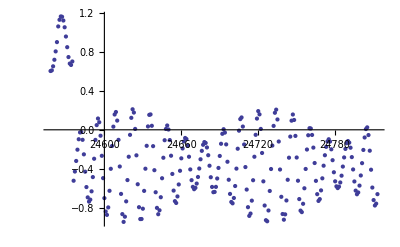

```mathematica
(Flatten[{
newmoonsPerl[[1-nmpBegLun+24550-5;;1-nmpBegLun+24800]],
},1]/. {{n_,rds_}:>{n,rds,(rdsFromN[n]-rds)/(24*60*60)}}) //(ListPlot[#/.{a_,b_,c_}->{a,c}])&
```

```mathematica
(Flatten[{
newmoonsPerl[[1-nmpBegLun+24550-5;;1-nmpBegLun+24580]],
},1]/. {{n_,rds_}:>{dateFromRDD[rds//daysFromSecs//N//Round//Rationalize],n,rds,(rdsFromN[n]-rds)/(24*60*60)}}) //MatrixForm
```

({{1986,8,5,0,0,0},24558,62659228565,0.60186}
{{1986,9,3,0,0,0},24559,62661779444,0.608387}
{{1986,10,3,0,0,0},24560,62664327296,0.649948}
{{1986,11,1,0,0,0},24561,62666872949,0.71696}
{{1986,11,30,0,0,0},24562,62669416985,0.802687}
{{1986,12,30,0,0,0},24563,62671960212,0.897778}
{{1987,1,28,0,0,0},24564,62674497794,1.05821}
{{1987,2,27,0,0,0},24565,62677043361,1.12621}
{{1987,3,28,0,0,0},24566,62679591859,1.1603}
{{1987,4,27,0,0,0},24567,62682143580,1.15708}
{{1987,5,26,0,0,0},24568,62684698334,1.11875}
{{1987,6,25,0,0,0},24569,62687255746,1.04967}
{{1987,7,25,0,0,0},24570,62689815375,0.95492}
{{1987,8,23,0,0,0},24571,62692376243,0.845833}
{{1987,9,22,0,0,0},24572,62694936428,0.744651}
{{1987,10,21,0,0,0},24573,62697493607,0.67826}
{{1987,11,20,0,0,0},24574,62700046301,0.663779}
{{1987,12,19,0,0,0},24575,62702594652,0.699565}
{{1988,1,19,0,0,0},24576,62705251576,-0.521282}
{{1988,2,18,0,0,0},24577,62707794887,-0.427163}
{{1988,3,18,0,0,0},24578,62710336973,-0.318866}
{{1988,4,17,0,0,0},24579,62712878438,-0.203381}
{{1988,5,16,0,0,0},24580,62715420659,-0.0966467}
{{1988,6,14,0,0,0},24581,62717966061,-0.0267294}
{{1988,7,14,0,0,0},24582,62720517218,-0.0234208}
{{1988,8,13,0,0,0},24583,62723075492,-0.102485}
{{1988,9,11,0,0,0},24584,62725639787,-0.251236}
{{1988,10,11,0,0,0},24585,62728206564,-0.428715}
{{1988,11,10,0,0,0},24586,62730771617,-0.58624}
{{1988,12,9,0,0,0},24587,62733332187,-0.691878}
{{1989,1,8,0,0,0},24588,62735887361,-0.735062}
{{1989,2,6,0,0,0},24589,62738437052,-0.714786}
{{1989,3,8,0,0,0},24590,62740981161,-0.629903}
{{1989,4,6,0,0,0},24591,62743520002,-0.484049}
{{1989,5,5,0,0,0},24592,62746055217,-0.296226}
{{1989,6,4,0,0,0},24593,62748590000,-0.103404}
Null)

#### Fiddle

```mathematica
{minDiff,maxDiff}=(fooCull[newmoonsPerl]/.{{n_,rds_}:>{(rdsFromN[n]-rds)/(24*60*60)}})//{Min[#],Max[#]}&
(-(minDiff+maxDiff)/2)+{minDiff,maxDiff}
(-(minDiff+maxDiff)/2)
```

{-0.952516,0.699565}

{-0.826041,0.826041}

0.126476

```mathematica
mqPerlAll[[All,{1,4}]]//Take[#,{100,200}]&;
```

#### Plot

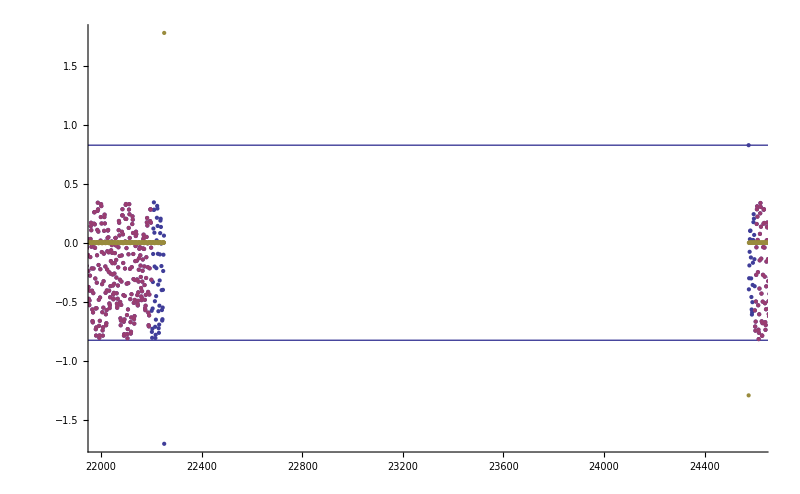

```mathematica
ListPlot[{
fooCull[ Transpose[{newmoonsKron[[All,1]],(newmoonsPerl[[All,2]]-newmoonsKron[[All,2]])} ]]
}, ImageSize->800];
Show[{
Plot[(-(minDiff+maxDiff)/2)+{minDiff,maxDiff}, {a,begLun,endLun}],
ListPlot[{
(fooCull[newmoonsPerl]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
(Select[mqPerlAll[[All,{1,4}]], (Not[22200<#[[1]]<24600])&]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
fooCull[ Transpose[{newmoonsKron[[All,1]],(newmoonsPerl[[All,2]]-newmoonsKron[[All,2]])/(24*60*60)} ]]
}]}, ImageSize->800, PlotRange->{{22000,24600},Automatic}]
```

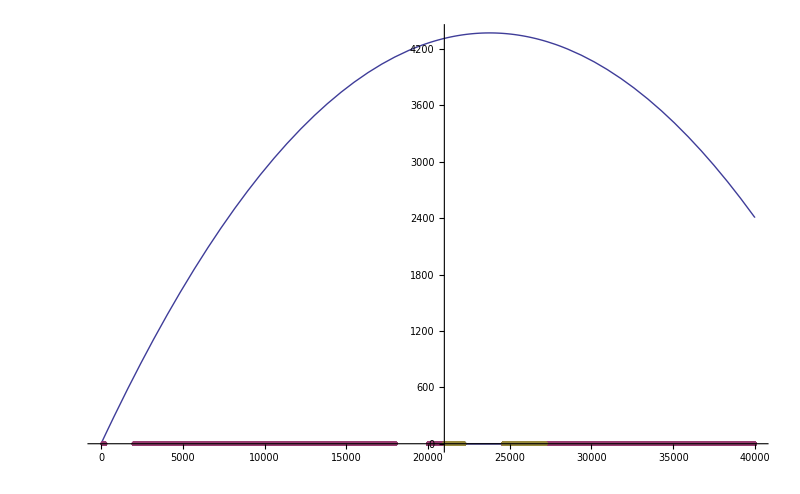

```mathematica
Show[{
Plot[(-(minDiff+maxDiff)/2)+{minDiff,maxDiff}, {a,begLun,endLun}],
Plot[rdsFromN[n]-rdsIntegratedFromN[n],{n,0,40000}],
ListPlot[{
(fooCull[newmoonsPerl]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
(Select[mqPerlAll[[All,{1,4}]], (Not[22200<#[[1]]<24600])&]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
fooCull[ Transpose[{newmoonsKron[[All,1]],(newmoonsPerl[[All,2]]-newmoonsKron[[All,2]])/(24*60*60)} ]]
}]}, ImageSize->800, PlotRange->{{0,40000},Automatic}]
```

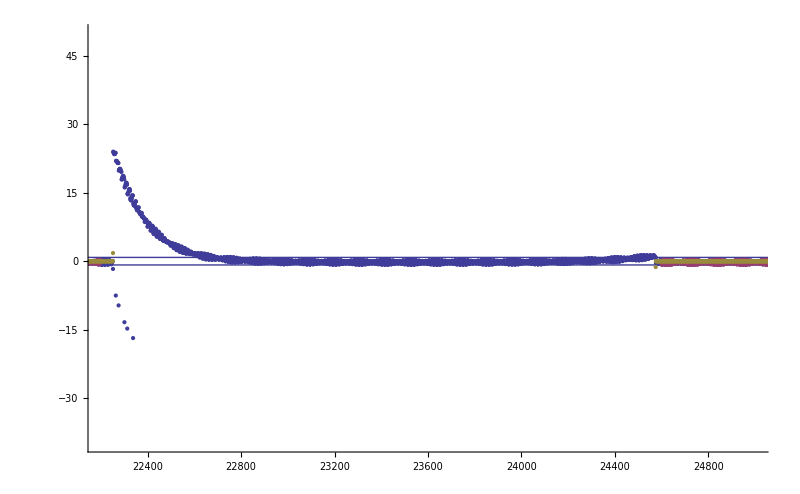

```mathematica
Show[{
Plot[(-(minDiff+maxDiff)/2)+{minDiff,maxDiff}, {a,begLun,endLun}],
Plot[rdsFromN[n]-rdsIntegratedFromN[n],{n,0,40000}],
ListPlot[{
(Identity[newmoonsPerl]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
(Select[mqPerlAll[[All,{1,4}]], (Not[22200<#[[1]]<24600])&]/.{{n_,rds_}:>{n,(-(minDiff+maxDiff)/2)+(rdsFromN[n]-rds)/(24*60*60)}}),
fooCull[ Transpose[{newmoonsKron[[All,1]],(newmoonsPerl[[All,2]]-newmoonsKron[[All,2]])/(24*60*60)} ]]
}]}, ImageSize->800, PlotRange->{{22200,25000},{-40,50}}]
```

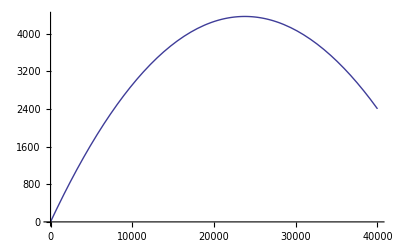

```mathematica
Plot[Evaluate[{rdsFromN[n]-rdsIntegratedFromN[n]}],{n,0,40000}]
```

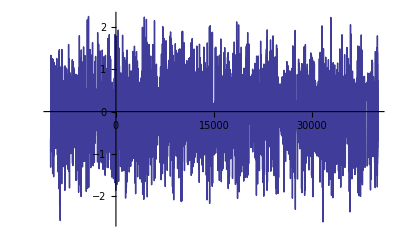

```mathematica
Plot[rdsIntegratedFromN[nIntegratedFromJD[jdFromRDS[a]]]-a, {a, -10000, 40000}]
```

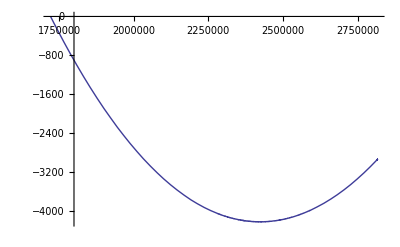

```mathematica
Plot[{nEstFromJD[jd]-nIntegratedFromJD[jd]}*28.5*24*60*60,{jd,jdFromDate[{1,1,1}],jdFromDate[{3000,1,1}]}]
```